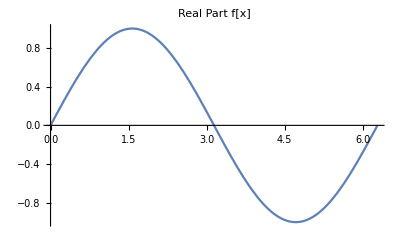

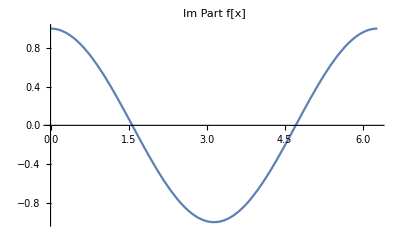

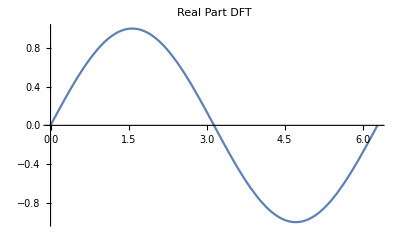

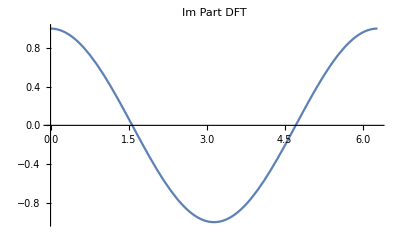

```mathematica
(* f is a complex-valued function defined on uniform partition of 0 to 2Pi.
Using Discrete Fourier Interpolation to determine fourier coefficients and numerically
verifying theorem from class stating that the size (using usual norm) of f evaluated at points along the partition and considered as an n-tuple in C^n is the same as the size (using semi-norm) of DF Interpolation of f*)

f[x_]:=Sin[x]+I*Cos[x];

n =5;
h = 2*Pi/n;
xvec = {};
For[i=0,i≤n-1,++i,
Subscript[x, i]=i*h;
AppendTo[xvec,Subscript[x, i]]
];

If[EvenQ[n],
Subscript[m, 0]= n/2;
Subscript[m, 1]=n/2,
Subscript[m, 0]=(n-1)/2;
Subscript[m, 1]=(n+1)/2
];

coef = {};
For[k=-Subscript[m, 0],k≤Subscript[m, 1]-1,++k,
Subscript[C, k]=(1/n)*∑_(i=0)^(n-1) f[Subscript[x, i]]*Exp[-I*k*Subscript[x, i]];
AppendTo[coef,Subscript[C, k]]
];

DFT[x_]:=∑_(k=-Subscript[m, 0])^(Subscript[m, 1]-1) Subscript[C, k] Exp[I*k*x]
Plot[Re[f[x]],{x, 0, 2*Pi},PlotLabel->"Real Part f[x]"]
Plot[Im[f[x]],{x,0,2*Pi},PlotLabel->"Im Part f[x]"]
Plot[Re[DFT[x]],{x,0,2*Pi},PlotLabel->"Real Part DFT"]
Plot[Im[DFT[x]],{x,0,2*Pi},PlotLabel->"Im Part DFT"]
```

```mathematica
N[Norm[f[xvec]],10]  (* comparing norm of f as n-tuple to semi-norm of DFInterpolation of f*)
```

2.236067977

```mathematica
N[Sqrt[n*∑_(k=-Subscript[m, 0])^(Subscript[m, 1]-1) Subscript[C, k]*Conjugate[Subscript[C, k]]],10]
```

2.236067977+0. ⅈ

{{0,1},{10,0},{20,-1},{30,0},{40,1},{50,0},{60,-1},{70,0},{80,1},{90,0}}

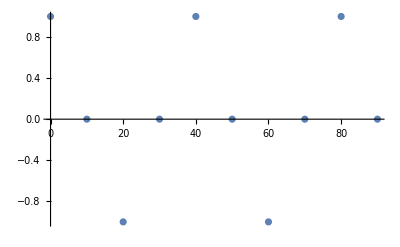

```mathematica
(* Messing around with Discrete Fourier Interpolation *)

Clear["Global`*"]

(* f 10-tuple {1,0,-1,0,1,0,-1,0,1,0} defined on uniform partition of [0,100] where delatx = 10 *)
ftuple = {1, 0, -1, 0, 1, 0, -1, 0, 1, 0};
fpoints = Table[{10*(i-1),Sin[Pi/2*i]},{i,1,10}]
ListPlot[fpoints]
```

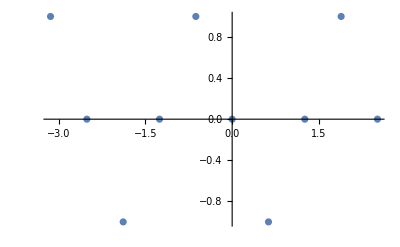

```mathematica
n = 10;
a1 = 0;
b1 = 100;
deltax = (b1-a1)/n;

(* change of variable function *)
g[x_,a_,b_]:=((2*Pi)/(b-a))*(x-a)-Pi;

xvec = Table[10*i,{i,0,9}]; (* original domain, [0,100] partioned uniformly with delta x = 10 *)
xvecshift = g[xvec, a1, b1];  (* shifted and scaled domain, [-Pi, Pi] partioned uniformly with deltax = 2Pi/10 *)

fshiftpoints = Table[{xvecshift[[i]], Sin[Pi/2*i]},{i,1,10}]; (* assigning values of f as 10-tuple to appropriate points of shifted domain *);
ListPlot[fshiftpoints]
```

```mathematica
If[EvenQ[n],
Subscript[m, 0]= n/2;
Subscript[m, 1]=n/2,
Subscript[m, 0]=(n-1)/2;
Subscript[m, 1]=(n+1)/2
];

coef = {};
For[k=-Subscript[m, 0],k≤Subscript[m, 1]-1,++k,
Subscript[C, k]=(1/n)*∑_(i=0)^(n-1) ftuple[[i+1]]*Exp[-I*k*xvecshift[[i+1]]];
AppendTo[coef,Subscript[C, k]]
];

DFT[x_]:=∑_(k=-Subscript[m, 0])^(Subscript[m, 1]-1) Subscript[C, k] Exp[I*k*x]

DFTpoints = Table[{xvecshift[[i]],Simplify[DFT[xvecshift[[i]]]]},{i,1,10}];

(* Here we see that the Discrete Fourier Interpolation, evaluated at points along the partition {-Pi, -4Pi/5, -3Pi/5, ........ 4Pi/5, Pi} produces the same values of the 10-tuple {f[0], f[10], f[20], ....... f[80], f[90]} = {1, 0, -1, 0, 1, 0, -1, 0, 1, 0} *)
ListPlot[DFTpoints]
```

-Graphics-